```mathematica
selection[words_] = 8728.080373902008-0.8400752435385844words+0.000019949689271781237 words^2;
quick[words_] = 15.057946764996796+0.001671169675241757 words-2.9212801881317814*10^-9 words^2;
merge[words_] =12.807590932610985+0.0007973480826874573 words+1.2051340206162585*10^-10 words^2;
insertion[words_] = 4910.039017276736-0.4887349709532982 words+0.000011012226464628218 words^2;
bubble[words_] = 14164.567389739186-1.100396645066854 words+0.00003519432450389842 words^2;
```

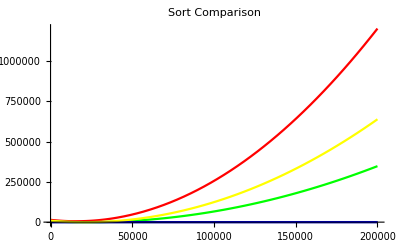

```mathematica
Show[ Plot[bubble[words], {words, 0, 200000}, PlotStyle->Red], Plot[insertion[words], {words, 0, 200000}, PlotStyle->Green], Plot[merge[words], {words, 0, 200000}, PlotStyle->Black], Plot[quick[words], {words,0, 200000}, PlotStyle->Blue],Plot[selection[words], {words, 0, 200000}, PlotStyle->Yellow], PlotLabel->"Sort Comparison"]

Show[ Plot[merge[words], {words, 0, 200000}, PlotStyle->Black], Plot[quick[words], {words,0, 200000}, PlotStyle->Blue], PlotLabel->"MergeSort v. QuickSort Comparison"]
```